```mathematica
ClearAll["Global`*"]
```

```mathematica
startpos =lokace["Cheb"]
endpos=lokace["Ostrava"]
startcas=DateObject[{2021,4,12,6}]
```

{50.08,12.35}

{49.83,18.27}

Hour beginning: Mon 12 Apr 2021 6 amGMT+2

```mathematica
V = 9;
lokace[mesto_]:=CityData[mesto,"Coordinates"]
CzechRep=Entity["Country","CzechRepublic"];
CzechiaContour = Graphics[{EdgeForm[Thick], Lighter[LightGray],CountryData["Czech Republic", "Polygon"]}, ImageSize->Large, AspectRatio->0.55];
CzechiaContour2 = GeoGraphics[{EdgeForm[Thin],FaceForm[],CountryData["Czech Republic", "Polygon"]}, ImageSize->Large, AspectRatio->0.55];
dg={111132.95,111319.49*Cos[50Degree]};
u[x_,y_]:=wind[x,y].{1,0}
v[x_,y_]:=wind[x,y].{0,1}
dfdx[x_,y_]:=Evaluate[D[wind[x,y],{x,1}]]
dfdy[x_,y_]:=Evaluate[D[wind[x,y],{y,1}]]
dudx[x_,y_]:=dfdx[x,y].{1,0}
dudy[x_,y_]:=dfdy[x,y].{1,0}
dvdx[x_,y_]:=dfdx[x,y].{0,1}
dvdy[x_,y_]:=dfdy[x,y].{0,1}
eqs={x'[t]==V Cos[β[t]]+u[x[t],y[t]],y'[t]==V Sin[β[t]]+v[x[t],y[t]],β'[t]==dvdx[x[t],y[t]]Sin[β[t]]^2+(dudx[x[t],y[t]]-dvdy[x[t],y[t]])Sin[β[t]]Cos[β[t]]-dudy[x[t],y[t]]Cos[β[t]]^2};
```

InterpolatingFunction::dmval: Input value {16902.7,17415.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

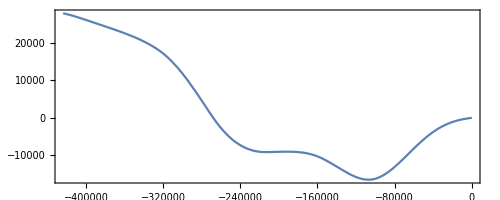

-Graphics-

```mathematica
CzechiaGrid = Flatten[CoordinateBoundsArray[GeoBounds[CzechRep], 0.8],1];
CzechiaGridWindData=WindVectorData[CzechiaGrid, startcas,"DownwindGeoVectorENU"];
CzechiaGridWindData["Vector"];
CzechiaGridWindData2=SynthesizeMissingValues[CzechiaGridWindData["Vector"],MissingValuePattern->Missing["NotAvailable"]];
CzechiaGridmetr={(#[[2]]-endpos[[2]])*dg[[2]],(#[[1]]-endpos[[1]])*dg[[1]]}&/@CzechiaGrid;
CzechiaGridWind=QuantityMagnitude[UnitConvert[CzechiaGridWindData2,"m/s"]];
Transpose[{CzechiaGridmetr,CzechiaGridWind}];
wind=Interpolation[Transpose[{CzechiaGridmetr,CzechiaGridWind}] ];
x0={((startpos-endpos)*dg)[[2]],((startpos-endpos)*dg)[[1]]};
sol=ParametricNDSolve[Join[eqs,{x[0]==x0[[1]],y[0]==x0[[2]],β[0]==β0}],{x,y,β},{t,0,16*3600},{β0}];
{x[β0][t],y[β0][t]}/.sol;
koreny=FindRoot[{x[β0][tend]==0,y[β0][tend]==0}/.sol,{{β0,0.3},{tend,15*3600}},Method->"Secant"];
β0=koreny[[1,2]];
tend =koreny[[2,2]];
sol2=NDSolve[Join[eqs,{x[0]==x0[[1]],y[0]==x0[[2]],β[0]==β0}],{x,y,β},{t,0,tend}];
CzechiaStreamPlot=GeoStreamPlot[CzechiaGridWindData, GeoBackground->"StreetMap", VectorColorFunction->None, VectorStyle->RGBColor[0.5,0.26,0.93]]
ParametricPlot[{x[t],y[t]}/.sol2,{t,0,tend},Frame->True]
trajectory=ParametricPlot[{x[t]/dg[[2]]+endpos[[2]],y[t]/dg[[1]]+endpos[[1]]}/.sol2,{t,0,tend},PlotStyle->Yellow];
Show[CzechiaContour2,trajectory,PlotRange->Automatic,AspectRatio->0.55,Axes->False]
```